```mathematica
NSolve[.01 Exp[x]==1+(.01)/(1+x),x,Reals]
```

{{x→-1.01004},{x→4.60695}}

```mathematica
Plot[.01 Exp[x]=1+(.01)/(1+x),{x,-5,5},Range[-5,5]]
```

Plot::nonopt: Options expected (instead of Range[-5,5]) beyond position 2 in Plot[0.01 Exp[x]=1+0.01/(1+x),{x,-5,5},Range[-5,5]]. An option must be a rule or a list of rules.

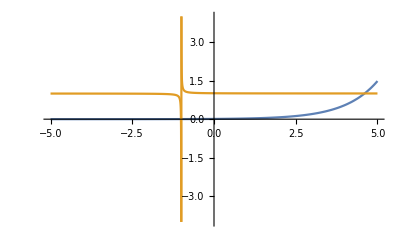

```mathematica
Plot[{0.01 Exp[x],1+0.01/(1+x)},{x,-5,5},PlotRange->4]
```

```mathematica
Log[.01]
```

```mathematica
-4.605170185988091

DSolve[{ϵ u''[t]+2t u'[t]==t^3,u[0]==0,u'[0]==1/ϵ},u[t],{t,0,1}]
```

-4.60517

{{u[t]→(2 t (t^2-3 ϵ) √ϵ+3 √π (2+ϵ^2) Erf[t/(√ϵ)])/(12 √ϵ)}}

```mathematica
{{u[t]->(2 t (t^2-3 ϵ) √ϵ+3 √π (2+ϵ^2) Erf[t/(√ϵ)])/(12 √ϵ)}}⟦1,1,2⟧
```

```mathematica
ϵ:=.01
```

```mathematica
Clear[ϵ]
```

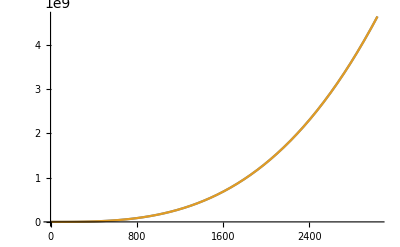

```mathematica
Plot[{(2 t (t^2-3 ϵ) √ϵ+3 √π (2+ϵ^2) Erf[t/(√ϵ)])/(12 √ϵ),t^3/6+Sqrt[π]/(2Sqrt[ϵ])Erf[t/Sqrt[ϵ]]},{t,0,3030},PlotRange->Full]
```

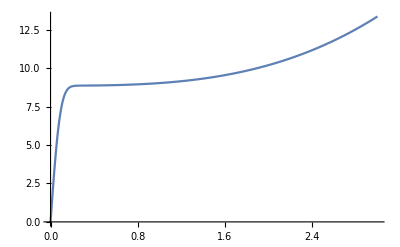

```mathematica
Plot[t^3/6+Sqrt[π]/(2Sqrt[ϵ])Erf[t/Sqrt[ϵ]],{t,0,3},PlotRange->Full]
```

```mathematica
NDSolve[{(1+ϵ)x^2y'[x]==ϵ((1-ϵ)x(y[x])^2-(1+ϵ)x+(y[x])^3+2ϵ (y[x])^2),y[1]==1},y[x],{x,0,1}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {x,y[x]} = {0.,1.70707×10^-7}.

{{y[x]→                                  -15
InterpolatingFunction[{{2.08461 10   , 1.}}, <>][x]}}

```mathematica
y0=1
```

1

```mathematica
Clear[y1]
```

```mathematica
y1=1-1/x
```

1-1/x

```mathematica
Clear[ϵ]
```

```mathematica
Expand[(1+ϵ)x^2(ϵ y1'+ϵ^2 y2')==ϵ((1-ϵ)x(y0+ϵ y1+ϵ^2 y2)^2-(1+ϵ)x+(y0+ϵ y1+ϵ^2 y2)^3+2ϵ (y0+ϵ y1+ϵ^2 y2)^2)]
```

x^2 ϵ y1'+x^2 ϵ^2 y1'+x^2 ϵ^2 y2'+x^2 ϵ^3 y2'==ϵ+2 ϵ^2-2 x ϵ^2+3 y1 ϵ^2+2 x y1 ϵ^2+4 y1 ϵ^3-2 x y1 ϵ^3+3 y1^2 ϵ^3+x y1^2 ϵ^3+3 y2 ϵ^3+2 x y2 ϵ^3+2 y1^2 ϵ^4-x y1^2 ϵ^4+y1^3 ϵ^4+4 y2 ϵ^4-2 x y2 ϵ^4+6 y1 y2 ϵ^4+2 x y1 y2 ϵ^4+4 y1 y2 ϵ^5-2 x y1 y2 ϵ^5+3 y1^2 y2 ϵ^5+3 y2^2 ϵ^5+x y2^2 ϵ^5+2 y2^2 ϵ^6-x y2^2 ϵ^6+3 y1 y2^2 ϵ^6+y2^3 ϵ^7

```mathematica
\right
```

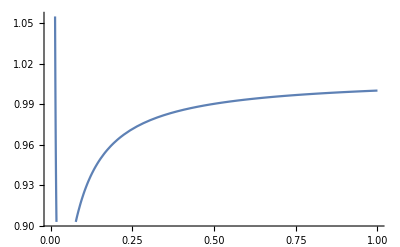

```mathematica
Plot[1+ϵ(1-1/x)+ϵ^2(3/(2x^2)-2/x+Log[x]+1/2),{x,0,1}]
```

```mathematica
Expand[(v0+a v1)^2]
```

v0^2+2 a v0 v1+a^2 v1^2

```mathematica
Integrate[Sqrt[2+x]/x^(3/2)-(2+x)^(3/2)/x^(5/2)+(2Sqrt[2+x])/x^(5/2)-1/x^4,x]
```

1/(3 x^3)

```mathematica
ϵ=.01
```

0.01

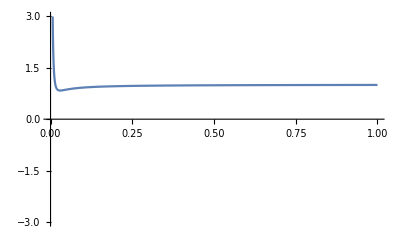

```mathematica
Plot[{1+ϵ(1-1/x)+ϵ^2(3/(2x^2)-2/x+1/2)},{x,0,1},PlotRange->3]
```

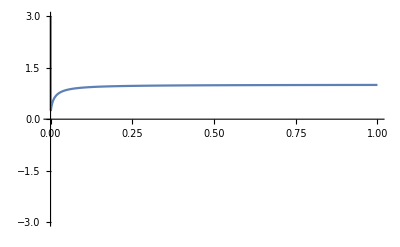

```mathematica
Plot[Sqrt[x/(2ϵ+x)]+ϵ+ϵ^4/(3(x^2+2x ϵ)^(3/2)),{x,0,1},PlotRange->3]
```

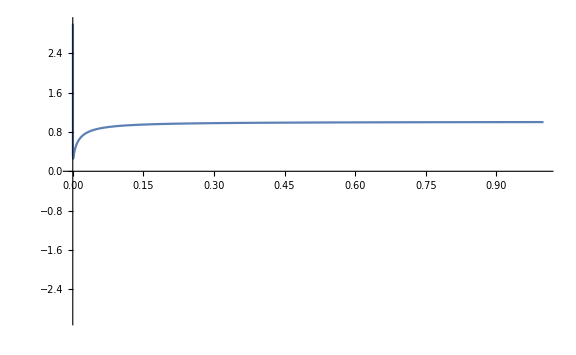

```mathematica
Show[%33,ImageSize->Large]
```

```mathematica
-1-Log[.01]-.01
```

3.59517

```mathematica
ϵ=.01
```

0.01

```mathematica
-Log[ϵ]-Log[(1-Log[ϵ]+ϵ)/(ϵ(1-Log[ϵ]))]-Log[(1-Log[(ϵ(1-Log[ϵ]))/(1=Log[ϵ]+ϵ)]+ϵ)/(ϵ(1-Log[(ϵ(1-Log[ϵ]))/(1-Log[ϵ]+ϵ)]))]
```

Set::setraw: Cannot assign to raw object 1.

-4.71738+0.525588 ⅈ

```mathematica
-Log[ϵ]
```

4.60517

```mathematica
Expand[Log[(1-Log[ϵ]+ϵ)/(ϵ(1-Log[ϵ]))]]
```

4.60695

```mathematica
Clear[ϵ]
```

```mathematica
Log[(1-Log[(ϵ(1-Log[ϵ]))/(1=Log[ϵ]+ϵ)]+ϵ)/(ϵ(1-Log[(ϵ(1-Log[ϵ]))/(1-Log[ϵ]+ϵ)]))]
```

Set::setraw: Cannot assign to raw object 1.

-4.7156+0.525588 ⅈ

```mathematica
ϵ=.01
```

0.01

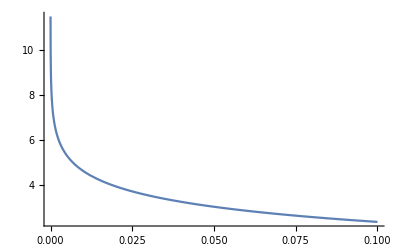

```mathematica
Plot[-Log[(ϵ(1-Log[(ϵ(1-Log[ϵ]))/(1-Log[ϵ]+ϵ)]))/(1-Log[(ϵ(1-Log[ϵ]))/(1-Log[ϵ]+ϵ)]+ϵ)],{ϵ,.00001,.1},PlotRange->Full]
```

```mathematica
NSolve[Tan[x]==1/(.01)]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.5608}}

```mathematica
π/2-.01-.01^3 2/3
```

1.5608

```mathematica
Expand[(1-1/ξ+3/(2ξ^2))^2]
```

1+9/(4 ξ^4)-3/ξ^3+4/ξ^2-2/ξ

```mathematica
Simplify[1/(-2(1-1/ξ+3/(2 ξ^2))^2)]
```

```mathematica
Expand[-(2 ξ^4)/((3-2 ξ+2 ξ^2)^2)]
```

-(2 ξ^4)/((3-2 ξ+2 ξ^2)^2)

```mathematica
Simplify[ξ/(2-(4ξ^4)/((3-2ξ+2ξ^2)^2))]
```

ξ/(2-(4 ξ^4)/((3-2 ξ+2 ξ^2)^2))

```mathematica
Simplify[(x(3-2x+2x^2)^2)/(2(3-2x+2x^2)^2-4x^4)]
```

(x (3-2 x+2 x^2)^2)/(-4 x^4+2 (3-2 x+2 x^2)^2)

```mathematica
Clear[y0]
```

```mathematica
D[y0,x]
```

(-x/(2+x)^2+1/(2+x))/(2 √(x/(2+x)))

```mathematica
FullSimplify[(-x/(2+x)^2+1/(2+x))/(2 √(x/(2+x)))]
```

1/(√x (2+x)^(3/2))

```mathematica
Expand[(1+ϵ)x^2(y0'+ϵ y1')==(1-ϵ)ϵ x (y0+ϵ y1)^2-(1+ϵ)ϵ x+(y0+ϵ y1)^3+2ϵ (y0+ϵ y1)^2]
```

x^2 y0'+x^2 ϵ y0'+x^2 ϵ y1'+x^2 ϵ^2 y1'==y0^3-x ϵ+2 y0^2 ϵ+x y0^2 ϵ+3 y0^2 y1 ϵ-x ϵ^2-x y0^2 ϵ^2+4 y0 y1 ϵ^2+2 x y0 y1 ϵ^2+3 y0 y1^2 ϵ^2-2 x y0 y1 ϵ^3+2 y1^2 ϵ^3+x y1^2 ϵ^3+y1^3 ϵ^3-x y1^2 ϵ^4

```mathematica
DSolve[y'[x]-3/(x(2+x))y[x]==-1/(Sqrt[x](2+x)^(3/2)),y[x],x]
```

{{y[x]→ⅇ^(3 (Log[x]/2-1/2 Log[2+x]))/x+ⅇ^(3 (Log[x]/2-1/2 Log[2+x])) C[1]}}

```mathematica
Simplify[{{y[x]->ⅇ^(3 (Log[x]/2-1/2 Log[2+x]))/x+ⅇ^(3 (Log[x]/2-1/2 Log[2+x])) C[1]}}]
```

{{y[x]→(√x (1+x C[1]))/(2+x)^(3/2)}}

```mathematica
□_□
```

```mathematica
Expand[{{y[x]->(2+x) (1/(2+x)-√(2+x) ((√x)/(3 (2+x)^2)+(√x)/(3 (2+x))))+(2+x) C[1]}}]
```

{{y[x]→-(2 √x)/(3 (2+x)^(3/2))-x^(3/2)/(3 (2+x)^(3/2))+2/(2+x)+x/(2+x)-(2 √x)/(3 √(2+x))-x^(3/2)/(3 √(2+x))+2 C[1]+x C[1]}}

```mathematica
y0=Sqrt[x/(2+x)]
```

√(x/(2+x))

```mathematica
FullSimplify[x^2D[y0,x]+x^2y1'==-x+2(y0)^2+x y0^2+3y0^2y1]
```

(x (√(x/(2+x))-3 y1+x (2+x) y1'))/(2+x)==0

```mathematica
ClearAll
```

ClearAll

```mathematica
ϵ=.01
```

0.01

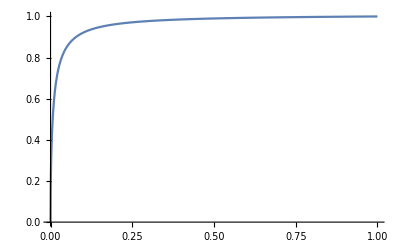

```mathematica
Plot[Sqrt[x/(2ϵ+x)]+ϵ Sqrt[x](ϵ+x)/(2ϵ+x)^(3/2)+.5 ϵ^2,{x,0,1},PlotRange->Full]
```

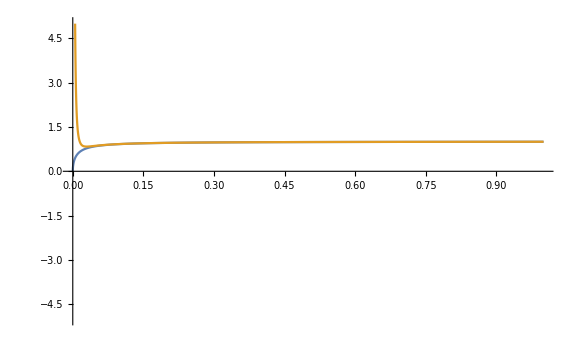

```mathematica
Show[%81,ImageSize->Large]
```

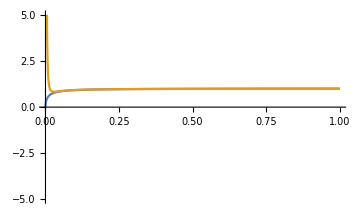

```mathematica
Show[%85,ImageSize->Medium]
```

```mathematica
Clear[ϵ]
```

```mathematica
Limit[ϵ Sqrt[x](ϵ+x)/(2ϵ+x)^(3/2),ϵ->0]
```

0

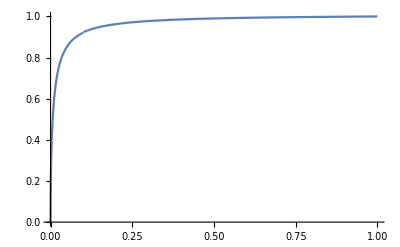

```mathematica
Plot[Piecewise[{{Sqrt[x/(2ϵ+x)]+ϵ Sqrt[x](ϵ+x)/(2ϵ+x)^(3/2),0<x<10ϵ},{1+ϵ(1-1/x)+ϵ^2(3/(2x^2)-2/x+1/2),10ϵ<x<1}}],{x,0,1},PlotRange->Full]
```